Using the τ non-dimensionalization of the hydrodynamic model, analytically solve for critical activity with respect to γ̇ under the assumption that k=l=0

```mathematica
Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((1+σ τ)/(γd τ)Subscript[λ, 2]-Subscript[λ, 1]),σ]/.{Subscript[λ, 1]->(γd τ λ)/(1+(γd τ)^2),Subscript[λ, 2]->λ/(1+(γd τ)^2)}
```

{{σ→(-2 η τ+(a λ τ^2)/(1+γd^2 τ^2)-τ^2 √(-4 γd^2 η^2+(a^2 λ^2)/((1+γd^2 τ^2)^2)-(4 a γd^2 η λ τ)/(1+γd^2 τ^2)))/(2 η τ^2)},{σ→(-2 η τ+(a λ τ^2)/(1+γd^2 τ^2)+τ^2 √(-4 γd^2 η^2+(a^2 λ^2)/((1+γd^2 τ^2)^2)-(4 a γd^2 η λ τ)/(1+γd^2 τ^2)))/(2 η τ^2)}}

```mathematica
SubMinus[σ]=(-2 η τ+(a λ τ^2)/(1+γd^2 τ^2)-τ^2 √(-4 γd^2 η^2+(a^2 λ^2)/((1+γd^2 τ^2)^2)-(4 a γd^2 η λ τ)/(1+γd^2 τ^2)))/(2 η τ^2)/.{η->1,τ->1,λ->1};
SubPlus[σ]=(-2 η τ+(a λ τ^2)/(1+γd^2 τ^2)+τ^2 √(-4 γd^2 η^2+(a^2 λ^2)/((1+γd^2 τ^2)^2)-(4 a γd^2 η λ τ)/(1+γd^2 τ^2)))/(2 η τ^2)/.{η->1,τ->1,λ->1};
```

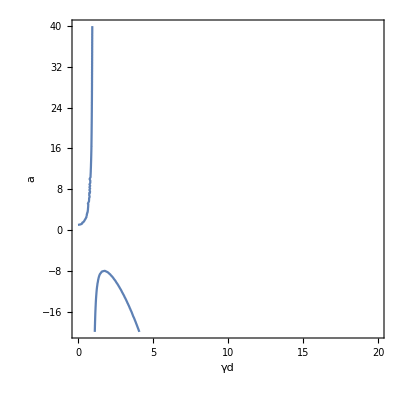

```mathematica
p1=ContourPlot[SubMinus[σ]==0,{γd,0,20}, {a,-20,40},AxesLabel->Automatic];
p2=ContourPlot[SubPlus[σ]==0,{γd,0,20}, {a,-20,20},AxesLabel->Automatic];
Show[p1,p2]
```